## Exploitation model Logistic with Type III functional response

```mathematica
Clear["Global`*"]
```

```mathematica
dNdt=r Ν(1-Ν/K)-c Ν^2 P/(b+ Ν^2)
```

r Ν (1-Ν/K)-(c P Ν^2)/(b+Ν^2)

Note that c (maximum consumption rate) is not defined.  It's our control parameter.

```mathematica
subparms={r->1, K->10,b->1, P->1};
```

```mathematica
equil=Solve[dNdt==0,Ν];equil//TableForm
equil2=equil[[All,1,2]]/.subparms;
```

Ν→0
Ν→K/3+(2^(1/3) (3 c K P r+3 b r^2-K^2 r^2))/(3 r (9 c K^2 P r^2-18 b K r^3-2 K^3 r^3+√(4 (3 c K P r+3 b r^2-K^2 r^2)^3+(9 c K^2 P r^2-18 b K r^3-2 K^3 r^3)^2))^(1/3))-((9 c K^2 P r^2-18 b K r^3-2 K^3 r^3+√(4 (3 c K P r+3 b r^2-K^2 r^2)^3+(9 c K^2 P r^2-18 b K r^3-2 K^3 r^3)^2))^(1/3))/(3 2^(1/3) r)
Ν→K/3-((1+ⅈ √3) (3 c K P r+3 b r^2-K^2 r^2))/(3 2^(2/3) r (9 c K^2 P r^2-18 b K r^3-2 K^3 r^3+√(4 (3 c K P r+3 b r^2-K^2 r^2)^3+(9 c K^2 P r^2-18 b K r^3-2 K^3 r^3)^2))^(1/3))+((1-ⅈ √3) (9 c K^2 P r^2-18 b K r^3-2 K^3 r^3+√(4 (3 c K P r+3 b r^2-K^2 r^2)^3+(9 c K^2 P r^2-18 b K r^3-2 K^3 r^3)^2))^(1/3))/(6 2^(1/3) r)
Ν→K/3-((1-ⅈ √3) (3 c K P r+3 b r^2-K^2 r^2))/(3 2^(2/3) r (9 c K^2 P r^2-18 b K r^3-2 K^3 r^3+√(4 (3 c K P r+3 b r^2-K^2 r^2)^3+(9 c K^2 P r^2-18 b K r^3-2 K^3 r^3)^2))^(1/3))+((1+ⅈ √3) (9 c K^2 P r^2-18 b K r^3-2 K^3 r^3+√(4 (3 c K P r+3 b r^2-K^2 r^2)^3+(9 c K^2 P r^2-18 b K r^3-2 K^3 r^3)^2))^(1/3))/(6 2^(1/3) r)

```mathematica
LineCols={{Orange,Dotted,Thickness[0.01]},{Red,Thickness[0.01]},{Blue,Thickness[0.01]},{Green, Dotted,Thickness[0.0075]}};
```

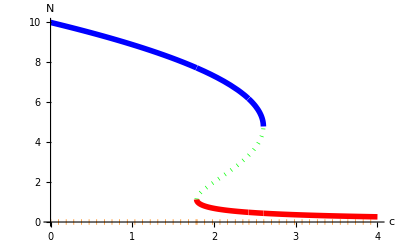

```mathematica
plot1=Plot[equil2,{c,0,4},AxesLabel->{c,Ν},PlotStyle->LineCols]
```

```mathematica
flambda=D[dNdt,Ν]
```

-(r Ν)/K+r (1-Ν/K)+(2 c P Ν^3)/((b+Ν^2)^2)-(2 c P Ν)/(b+Ν^2)

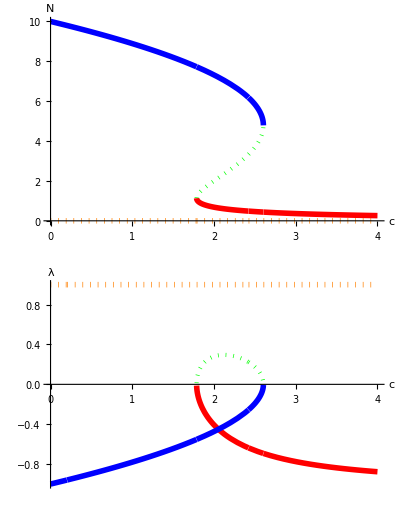

```mathematica
lambda=flambda/.equil/.subparms;
plot2=Plot[lambda,{c,0,4},PlotStyle->LineCols,AxesLabel->{c,λ}];
GraphicsGrid[{{plot1},{plot2}}]
```

```mathematica
pN=-Integrate[dNdt,Ν]
```

c P Ν-(r Ν^2)/2+(r Ν^3)/(3 K)-√b c P ArcTan[Ν/(√b)]

```mathematica
Manipulate[
GraphicsGrid[{ 
{
Plot[equil2,{c,0,4},AxesLabel->{c,Ν},PlotStyle->LineCols,GridLines->{{χ},None}],    
Plot[pN/.Join[subparms,{c->χ}],{Ν,0,10},AxesLabel->{"Ν","Φ"},Filling->Bottom]
}   ,{ 
Plot[lambda,{c,0,4},PlotStyle->LineCols,AxesLabel->{c,λ},GridLines->{{χ},None}]  
} }
],
{{χ,2.1,"c"},0,4,0.1}]
```

#### Include characteristic return time

```mathematica
RT=-1/flambda/.equil/.subparms;
```

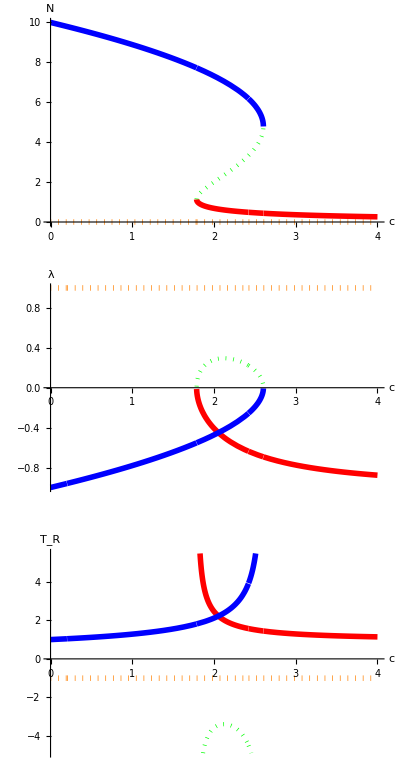

```mathematica
plot4=Plot[RT,{c,0,4},PlotStyle->LineCols,AxesLabel->{c,Subscript[T, R]}];
GraphicsGrid[{{plot1},{plot2},{plot4}}]
```

```mathematica
subparms2=Delete[subparms,3];
bmax=7;cmax=4;
Plot3D[{equil[[1,1,2]]/.subparms2,equil[[2,1,2]]/.subparms2,equil[[3,1,2]]/.subparms2,equil[[4,1,2]]/.subparms2},{c,0,cmax},{b,0,bmax},PlotStyle->{Orange,Red,Blue,Green},PlotRange->{Full,Full,{0,8}},AxesLabel->{"Max consumption (c)","Half saturation (b)","Ν"},PlotPoints->30]
```

-Graphics3D-